```mathematica
practicle 1
```

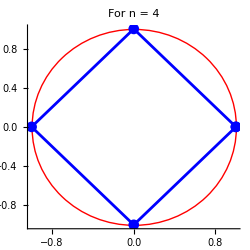

```mathematica
n=4;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 4"]
```

```mathematica
ClearAll;
```

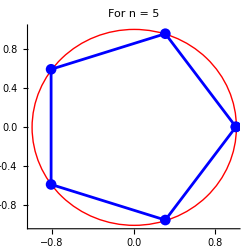

```mathematica
n=5;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 5"]
```

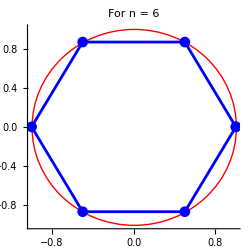

```mathematica
n=6;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 6"]
```

# Practicle 2

```mathematica
ClearAll;
```

```mathematica
Points = ComplexExpand[z /. Solve[z^3-8*I == 0]] 
Realpart=Re[Points];
Imaginarypart=Im[Points];
Data=Transpose[{Realpart,Imaginarypart}];
Data= Append[Data,Data[[1]]];
ListPlot[Map[Labeled[#,#]&, Data],PlotStyle->{PointSize[0.03]},PlotRange->{-3,2},ImageSize->300]
Show[Graphics[{Thick,Red,Circle[{0,0},2]}],ListLinePlot[Map[Labeled[#,#]&,Data],PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250]
```

{-2 ⅈ,ⅈ+√3,ⅈ-√3}

-Graphics-

-Graphics-

# Practical 3

## Write the parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal axis of 4 units and vertical minor axis of 2 units . Show the effect of rotation of this ellipse by an angel Pi/6 radians and shifting of the centre from (0, 0) to (2, 1), by making a parametric plot.

```mathematica
ClearAll;
```

```mathematica
A1 = ParametricPlot[{4*Cos[t], 2*Sin[t]},
{t, 0, 2*Pi}, Frame ->True , ImageSize -> 300, PlotLabel -> "Ellipse"]
```

-Graphics-

```mathematica
A2 = ParametricPlot[{4*Cos[t]*Cos[Pi/6]-2*Sin[t]*Sin[Pi/6],4*Cos[t]*Sin[Pi/6]+2*Sin[t]*Cos[Pi/6]},{t,0,2*Pi},Frame->True,ImageSize->300,PlotLabel->"Ellipse"]
```

-Graphics-

-Graphics-

```mathematica
ClearAll;
```

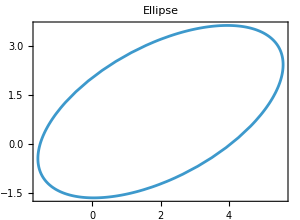

```mathematica
A3 = ParametricPlot [{4 * Cos [t] * Cos [Pi/6] - 2 * Sin [t] * Sin [Pi/6] + 2,
4 * Cos [t] * Sin [Pi/6] + 2* Sin [t] * Cos [Pi/6] +1},
{t, 0, 2* Pi}, Frame-> True, ImageSize -> 300, PlotLabel -> "Ellipse"]
```

# Practical 4

```mathematica
ClearAll;
```

```mathematica
Solve[w1==(3-4I)z1+(6+2I),z1]
```

{{z1→1/25 (-10+3 w1+2 ⅈ (-15+2 w1))}}

```mathematica
z=x+I*y;
A1=RegionPlot[Abs[z+(1+I)]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->300,PlotLabel->"Region: {z:|z+1+i|<1}"];
A2=RegionPlot[Abs[(1/25)(-10+3*z+2*I*(-15+2*z))+1+I]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->300,PlotLabel->"Region: {z:|z+1+i|<1}"];
Print[A1,A2]
```

-Graphics--Graphics-

```mathematica
Solve[w1==1/(z1+1),z1]
```

{{z1→(1-w1)/w1}}

```mathematica
z=x+I*y;
A1 = RegionPlot[Abs[z] < 1&&Im[z] > 0, {x,-2, 2}, {y,-2, 2}, Axes -> True, ImageSize -> 300, PlotLabel -> "Region: {z:|z|<1 and Im(z)>0}"];
A2 = RegionPlot[Abs[(1/z)-1] < 1&&Im[(1/z)-1] > 0, {x,-2, 2}, {y,-2, 2}, Axes -> True, ImageSize -> 300, PlotLabel -> "Image of the region: {z:|z|<1 and Im(z)>0}"];
Print[ A1, A2]
```

-Graphics--Graphics-

# Practical 5

```mathematica
ClearAll;
```

```mathematica
Solve[w1 == (-1+I)z1-2+3I, z1]
```

{{z1→1/2 (-5+ⅈ (1-w1)-w1)}}

```mathematica
z = x+I*y;
A1 = RegionPlot[Re[z] > 1, {x,-10, 10}, {y,-10, 10}, Axes -> True, ImageSize -> 300, PlotLabel -> "Region: {z:Re(z)>1}"];
A2 = RegionPlot[Re[(1/2)*(-5+I(1-z)-z)] > 1, {x,-10, 10}, {y,-10, 10}, Axes -> True, ImageSize -> 300, PlotLabel -> "Image of the region: {z:Re((1/2)*(-5+I(1-z)-z))>1}"];
Print[ A1, A2]
```

-Graphics--Graphics-

# Practical 6

```mathematica
ClearAll;
```

```mathematica
Solve[w1==1/z1,z1]
```

{{z1→1/w1}}

```mathematica
z=x+I*y;
A1=RegionPlot[Abs[z-1]≤1,{x,-2,2},{y,-2,2}, Axes->True,ImageSize->300,PlotLabel->"Region:{z:|z-1|<=1}"];
A2=RegionPlot[Re[1/z]≥1/2,{x,-2,2},{y,-2,2},Axes->True, ImageSize->300,PlotLabel->"Image ofthe region:{z: Re(z)>=1/2}"];
Print[ A1,A2]
```

-Graphics--Graphics-

# Practical 7

```mathematica
ClearAll;
```

```mathematica
z = x+I*y;
A1 = ContourPlot[{Re[z] ==-1, Re[z] ==-1/2, Re[z] == 1/2, Re[z] == 1, Im[z] ==-1, Im[z] ==-1/2, Im[z] ==1/2, Im[z] ==1}, {x,-2, 2}, {y,-2, 2}, Axes -> True, ImageSize -> 300];
A2 = ContourPlot[{Re[1/z] ==-1, Re[1/z] ==-1/2, Re[1/z] == 1/2, Re[1/z] ==1, Im[1/z] ==-1, Im[1/z] ==-1/2, Im[1/z] == 1/2, Im[1/z] == 1}, {x,-2, 2}, {y,-2, 2}, Axes -> True, ImageSize -> 300];
Print[ A1, A2]
```

-Graphics--Graphics-

# Practical 8

```mathematica
ClearAll;
```

```mathematica
C1[t_] = ComplexExpand[(-1+I)*(1-t)+(-1)*t] 
P1 = Show[ParametricPlot[{{Re[C1[t]], Im[C1[t]]}}, {t, 0, 1}, PlotStyle -> {Red, Thick}, AxesLabel -> {"Re(z)", "Im(z)"}], Graphics[{Red, Arrow[{{-1, 0.75}, {-1, 0}}]}]]
```

-1+ⅈ (1-t)

-Graphics-

```mathematica
C2[t_] = ComplexExpand[(-1)*(1-t)+(1+I)*t]
P1 = Show[ParametricPlot[{{Re[C2[t]], Im[C2[t]]}}, {t, 0, 1}, PlotStyle -> {Blue, Thick}, AxesLabel -> {"Re(z)", "Im(z)"}], Graphics[{Blue, Arrow[{{-1, 0}, {.7, .85}}]}]]
```

-1+(2+ⅈ) t

-Graphics-

```mathematica
C3[t_] = ComplexExpand[(1+I)*(1-t)+(3-I)*t]
P1 = Show[ParametricPlot[{{Re[C3[t]], Im[C3[t]]}}, {t, 0, 1}, PlotStyle -> {Green, Thick}, AxesLabel -> {"Re(z)", "Im(z)"}], Graphics[{Green, Arrow[{{1, 1}, {2, 0}}]}]]
```

1+ⅈ (1-2 t)+2 t

-Graphics-

```mathematica
Show[ParametricPlot[ {{Re[C1[t]], Im[C1[t]]}, {Re[C2[t]], Im[C2[t]]}, {Re[C3[t]], Im[C3[t]]}}, {t, 0, 1}, PlotStyle -> {{Red, Thick}, {Blue, Thick}, {Green, Thick}}, AxesLabel -> {"Re(z)", "Im(z)"}], 
Graphics[{Red, Arrow[{{-1, 0.75}, {-1, 0}}]}],
Graphics[{Blue, Arrow[{{-1, 0}, {1, 1}}]}],
Graphics[{Green, Arrow[{{1, 1}, {2, 0}}]}], PlotRange -> 2]
```

-Graphics-

# Practical 9

```mathematica
ClearAll;
```

```mathematica
Clear[z];
```

```mathematica
Integrate[Exp[z],{z,0,2+I*Pi/4}]
```

-1+(-1)^(1/4) ⅇ^2

```mathematica
ClearAll["Global`*"]

(* Define parametrization *)
z[t_] := t*(2 + (Pi/4)*I);

(* Extract real and imaginary parts for plotting *)
x[t_] := Re[z[t]];
y[t_] := Im[z[t]];

(* Plot the line segment *)
plot = ParametricPlot[
  {x[t], y[t]},
  {t, 0, 1},
  PlotStyle -> {Thick, Blue},
  Frame -> True,
  AxesLabel -> {"Re(z)", "Im(z)"},
  PlotRange -> All,
  GridLines -> Automatic,
  Epilog -> {
    Red, PointSize[Large], Point[{0, 0}],
    Black, Text["A (0,0)", {0, 0}, {-1, -1}],
    Red, Point[{2, Pi/4}],
    Black, Text["B (2, π/4)", {2, Pi/4}, {1, 1}]
  },
  PlotLabel -> "Line Segment L from A to B"
];

plot
```

-Graphics-

```mathematica
Integrate[z^2,{z,2+3*I,5+2*I}]
```

37+(133 ⅈ)/3

```mathematica
Integrate[Log[z],{z,2+3*I,5+2*I}]
```

(-3+ⅈ)-(2-5 ⅈ) ArcTan[2/5]+(3-2 ⅈ) ArcTan[3/2]-(1+(3 ⅈ)/2) Log[13]+(5/2+ⅈ) Log[29]

```mathematica
Integrate[Conjugate[z],{z,0,2+I}]
```

5/2

```mathematica
Integrate[(z+2)^2,{z,-2,-2+I}]
```

-ⅈ/3

# Practical 10

```mathematica
ClearAll;
```

```mathematica
ParametricPlot[{2+Cos[t], Sin[t]}, {t, 0, Pi}, PlotRange-> {{-1, 4}, {-2, 2}}, PlotStyle -> {Red, Thick}, ImageSize -> {250}]
```

-Graphics-

```mathematica
f[z_]:=1/(z-2);
z[t_]:=2+Cos[t]+ I*Sin[t];
Integrate[f[z[t]]*z'[t],{t,0,Pi}]
```

ⅈ π

```mathematica
ParametricPlot[{t, t^2}, {t,-1, 1}, PlotRange -> {{-1, 1}, {-1, 1}}, PlotStyle -> {Red, Thick}, ImageSize -> {250}] 
f[z_] := z-I;
z[t_] := t+I*t^2; Integrate[f[z[t]]*z'[t], {t,-1, 1}]
```

-Graphics-

0

# Practical 11

```mathematica
ClearAll;
```

```mathematica
Integrate[z, {z,-1-I, 3+I}]
```

4+2 ⅈ

```mathematica
f[z_]:=z;
z[t_]:=(t^2+2*t)+I*t;
Integrate[f[z[t]]*z'[t],{t,-1,1}]
```

4+2 ⅈ

```mathematica
A1 = ListLinePlot[{{Re[-1-I], Im[-1-I]}, {Re[3+I], Im[3+I]}}, ImageSize -> 300, GridLines -> Automatic, Frame -> True];
A2 = ContourPlot[{x == y^2+2*y}, {x,-2, 3}, {y,-3, 3}, Axes -> {True, True}, GridLines -> Automatic, ImageSize -> 300, Frame -> True, PlotLabel -> "Graph of x==y^2 + 2y"];
Show[ A1, A2]
```

-Graphics-

# Practical 12

```mathematica
ClearAll;
```

```mathematica
z0=2;
z1=2+i;
z[t_]=z0+t*(z1-z0);
Print["The parametric equation of the given curve is ,C:z[t] = ", ComplexExpand[z[t]],"where 0<t<=1, which represents straight line joining the points z0 = ",z0,"And z1= ", z1,"."];
p1=ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},
AxesStyle->Arrowheads[{-0.03,0.03}],AxesLabel->{"x", "y"},PlotStyle->{Thick,Green}, AxesOrigin->{0,0},
Ticks->{Range[-1,3,0.5],Range[-2,2.5,0.5]},PlotRange->{{-0.5,3},{-2,2}}];
p2=ListPlot[{{Re[z0],Im[z0]},{Re[z1],Im[z1]}},PlotStyle->{Thickness[0.09],Red}];
Show[p1,p2]
l=Integrate[Abs[z'[t]],{t,0,1}];
f[z_]=1/(z^2 + 1);
r=ComplexExpand[Re[f[z[t]]]];
i=ComplexExpand[Im[f[z[t]]]];
m=Maximize[{(r^2 +i^2)^(1/2),0≤t≤1},t];
ml=m[[1]]*1;
Print["Length of the arc is ,L = ", l, " and the value of M is ", m[[1]], "."]
Print["Using ML inequality , we have an upper bound for the given integral as ", ml, "."]
Manipulate[Show[ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->{Thick, Red}, PlotRange->2],ListLinePlot[{{{0,1},{Re[z[t]],Im[z[t]]}},{{0,-1},{Re[z[t]],Im[z[t]]}}},AxesOrigin->{0,0}]],{t,0,1}]
```

The parametric equation of the given curve is ,C:z[t] = 2where 0<t<=1, which represents straight line joining the points z0 = 2And z1= 2.

-Graphics-

Length of the arc is ,L = 0 and the value of M is 1/5.

Using ML inequality , we have an upper bound for the given integral as 1/5.

# Practical 13

```mathematica
z0 = 4;
z1 = 8+6*I;
L = z0+(z1-z0)t;
f[z_] := 1/(2*z^(1/2));
g[t_] := 4+(4+6*I)*t;
Integrate[f[g[t]]*g'[t], {t, 0, 1}]
ListLinePlot[{{Re[4], Im[4]}, {Re[8+6*I], Im[8+6*I]}}, ImageSize -> 350, GridLines -> Automatic, Frame -> True]
```

1+ⅈ

-Graphics-

# Practical 14

```mathematica
Grid[Table[{n,Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}], Frame->All] 
Plot[Evaluate[Table[{Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}]], {z,-3,3},PlotLegends->"Expressions"]
```

0 | 3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+(513 z^8)/512-(1023 z^9)/1024+(2049 z^10)/2048
2 | 1/3+(2-z)/9-1/(-2+z)+1/27 (-2+z)^2-1/81 (-2+z)^3+1/243 (-2+z)^4-1/729 (-2+z)^5+(-2+z)^6/2187-(-2+z)^7/6561+(-2+z)^8/19683-(-2+z)^9/59049+(-2+z)^10/177147
∞ | -513/z^10-255/z^9-129/z^8-63/z^7-33/z^6-15/z^5-9/z^4-3/z^3-3/z^2

-Graphics-

# Practical 15

```mathematica
f[z_]:=1/(5*z^4+26*z^2+5);
Print["f[z]=",f[z]]
Print[Denominator[f[z]]==0] 
solutionSet=Sort[Solve[Denominator[f[z]]==0,z]];
Print[solutionSet] 
Print["Thesingularities are"] 
z1=ReplaceAll[z,solutionSet[[1]]]; 
Print["z1=",z1] 
z2=ReplaceAll[z,solutionSet[[2]]]; 
Print["z2=",z2]
z3=ReplaceAll[z,solutionSet[[3]]]; 
Print["z3=",z3]
z4=ReplaceAll[z,solutionSet[[4]]]; 
Print["z4=",z4]
```

f[z]=1/(5+26 z^2+5 z^4)

5+26 z^2+5 z^4==0

{{z→-ⅈ/(√5)},{z→ⅈ/(√5)},{z→-ⅈ √5},{z→ⅈ √5}}

Thesingularities are

z1=-ⅈ/(√5)

z2=ⅈ/(√5)

z3=-ⅈ √5

z4=ⅈ √5

# Practical 16

```mathematica
f[z_] = Exp[2 /z]; 
residue = SeriesCoefficient[f[z], {z, 0,-1}];
Print["The residue of f(z) at the point z=0 is ",
residue, "."]
integral = 2Pi I*(residue);
Print["The value of  ⅇ^2/z ⅆz by cauchy residue theroem is : ", integral, "."]
```

The residue of f(z) at the point z=0 is 2.

The value of  ⅇ^2/z ⅆz by cauchy residue theroem is : 4 ⅈ π.

```mathematica
g[z_] = 1/(z^4 +z^3-2*z^2) ;
Apart[g[z]] 
residue0 = SeriesCoefficient[g[z], {z, 0,-1}];
residue1 = SeriesCoefficient[g[z], {z, 1,-1}];
residue2 = SeriesCoefficient[g[z], {z,-2,-1}];
Print["Residue of g(z) at z0 = 0 is ", residue0, ", at z1 = 1 is ",residue1, " and at z2 =-2 is ", residue2, "."] 
integral = 2Pi I*(residue0 +residue1 +residue2);
Print["The value of  1/ (z^4 + z^3 - 2*z^2) ⅆz by cauchy residue theroem is : ", integral]
```

1/(3 (-1+z))-1/(2 z^2)-1/(4 z)-1/(12 (2+z))

Residue of g(z) at z0 = 0 is -1/4, at z1 = 1 is 1/3 and at z2 =-2 is -1/12.

The value of  1/ (z^4 + z^3 - 2*z^2) ⅆz by cauchy residue theroem is : 0

# Practical 17

```mathematica
f[z_] := Exp[2/z];
h[z_] := (1/z^4)+z^3-2*z^2;
g[t_] := Cos[t]+I*Sin[t];
Integrate[f[g[t]]*g'[t], {t, 0, 2*Pi}] 
Integrate[h[g[t]]*g'[t], {t, 0, 2*Pi}]
```

Cloud::timelimit: This computation has exceeded the time limit for your plan.

$Aborted